# Random graphs with games

## Parameters

```mathematica
p=0.7;n=100;θ=1/(p n);
```

## Variables, Functions, Measures

```mathematica
(* conditional degree *)
K[g_,i_,l_]:=VertexDegree[g,l]AdjacencyMatrix[g]⟦VertexIndex[g,i],VertexIndex[g,l]⟧
iK[g_,i_,l_]:=Replace[Quiet[1./K[g,i,l]],q_?(!NumberQ@#&):>0]
(* normalization factor for the conditional degree *)
λ[g_,i_]:=Plus@@(K[g,i,#]&/@VertexList[g])
μ[g_,i_]:=Plus@@(iK[g,i,#]&/@VertexList[g])
(* normalized conditional degree *)
w[g_,i_,j_]:=With[{l=N@λ[g,i]},If[l>0,K[g,i,j]/l,0.]]
w[g_,i_]:=With[{l=N@λ[g,i]},If[l>0,(K[g,i,#]&/@VertexList[g])/l,0.]]
ncdMatrix[g_]:=w[g,#]&/@VertexList[g]
(* inverse normalized conditional degree *)
ζ[g_,i_,j_]:=With[{m=μ[g,i]},If[m>0,(iK[g,i,j])/m,0.]]
ζ[g_,i_]:=With[{m=μ[g,i]},If[m>0,(iK[g,i,#]&/@VertexList[g])/m,0.]]
incdMatrix[g_]:=ζ[g,#]&/@VertexList[g]
```

## Procedures

### Create a new graph

```mathematica
newgraph[]:=RandomGraph[BernoulliGraphDistribution[n,p],DirectedEdges->False];
newgraph[num_]:=RandomGraph[BernoulliGraphDistribution[n,p],num,DirectedEdges->False]
```

### Delete edges with weakest signals at each step

```mathematica
(*weakest[]:=
Module[{newgraph=graph},
Do[newgraph⟦i,j⟧=0;newgraph⟦j,i⟧=0,{i,1,n},{j,minids[i]}];
graph= newgraph;]*)
```

### Delete edges with signals below threshold

```mathematica
threshold[g_]:=
Module[{m},
(* m_ij will be 0 if the edge i->j should be deleted. This happens when either w_ij or w_ji is below θ. For this, we multiply the matrix by its transpose *)
m=Replace[ncdMatrix[g],c_?NumberQ:>If[c<θ,0,1],{2}];
m=m*Transpose@m;
AdjacencyGraph@Normal@m]
```

## Play

```mathematica
θ=95/(100p n)
```

0.0135714

```mathematica
graph=newgraph[];
gth=threshold[graph];
subg=Subgraph[gth,ConnectedComponents[gth]⟦1⟧];
Grid[Transpose@{
{"θ","Clustering Coefficient","Characteristic Path Length","Small World"},
With[{
cr=GlobalClusteringCoefficient[graph],
cth=GlobalClusteringCoefficient[subg],
lr=Plus@@Flatten@GraphDistanceMatrix[graph]/(n(n-1))//N,
lth=Plus@@Flatten@GraphDistanceMatrix[subg]/(VertexCount[subg](VertexCount[subg]-1))
},
{
{θ,Mean@DeleteCases[Flatten[ncdMatrix[graph]],0.]},
{cr,cth},
{lr,lth},
{(cr/Mean@crand)/(lr/Mean@lrand),(cth/Mean@crand)/(lth/Mean@lrand)}
}//N
]}]
```

θ | {0.0135714,0.0143513}
Clustering Coefficient | {0.702578,0.564029}
Characteristic Path Length | {1.29616,2.12545}
Small World | {1.00788,0.493425}

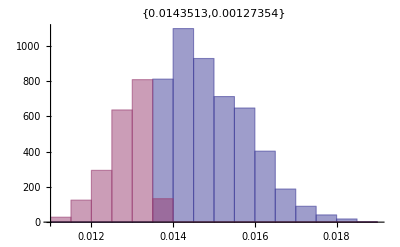

```mathematica
data=DeleteCases[Flatten@ncdMatrix[graph],0.];
Histogram[GatherBy[data,#<θ&],{0.0005},PlotLabel->{Mean@data,StandardDeviation@data}]
```

```mathematica
EdgeCount/@{graph,gth}
```

{3484,1458}

```mathematica
Grid[{{graph,gth,subg}}]
```

-Graphics- | -Graphics- | -Graphics-

## Stats

```mathematica
{crand,lrand}=Transpose@RandomVariate[GraphPropertyDistribution[{GlobalClusteringCoefficient[gr],Plus@@Flatten@GraphDistanceMatrix[gr]/(n(n-1))},gr\[Distributed]BernoulliGraphDistribution[n,p]],500]//N;//AbsoluteTiming
```

{0.24771,Null}

```mathematica
swth=
Table[
graph=newgraph[];
gth=threshold[graph];
subg=Subgraph[gth,ConnectedComponents[gth]⟦1⟧];
With[{ns=VertexCount[subg]},
(GlobalClusteringCoefficient[subg]/Mean@crand)/((Plus@@Flatten@GraphDistanceMatrix[subg]/(ns(ns-1)))/Mean@lrand)
],
{500}]//N;//AbsoluteTiming
```

{647.10293,Null}

```mathematica
Mean@swth
```

0.863051